```mathematica
m=12;(*in GeV*)
```

```mathematica
Λ=(0.91*m^(1/3)+0.3)*5(*in GeV^-1*);
```

```mathematica
ei=3/(2*m*Λ^2)(*in GeV*)//ScientificForm
```

8.80204×10^-4

```mathematica
er[mx_]:=(mx^2*m)/(m+mx)^2*(10^-2)^2(*in GeV*)
```

```mathematica
helm=Exp[(-er[10^8])/ei]
```

0.25581

```mathematica
er[10^8]//N
```

0.0012

```mathematica
HBARC=0.197327;
vesc=0.01;
A=6.0;
RA=(1.23 A^(1/3)-0.6)(*fm*);
r0=0.52 (*fm*);
s=0.9(*fm*);
R1=√(RA^2+7/3 π^2 r0^2-5 s^2)(*fm*);
Hsqr[q_]:=(3 SphericalBesselJ[1,(q R1)/HBARC]/((q R1)/HBARC))^2 Exp[-(q s/HBARC)^2]
```

```mathematica
q[mdm_]:=√2(m mdm)/(mdm+m)vesc
```

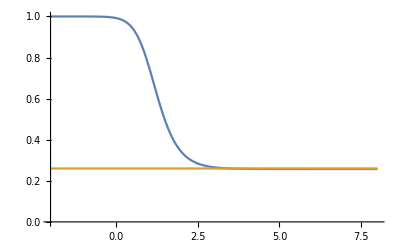

```mathematica
Plot[{Hsqr[q[10^x]],0.26},{x,-2,8},AxesOrigin->{-2,0},PlotRange->Full]
```

```mathematica
Hsqr[q[10]]
```

0.760609